# Device Physics

This notebook will be used for me to get a better understanding of some of the basic physics that occur within a device

## Constants

These are physical constants

```mathematica
kJ=QuantityMagnitude[UnitConvert[Null,"SIBase"]];
keV= QuantityMagnitude[UnitConvert[Null,"eV/K"]];
q =QuantityMagnitude[UnitConvert[Null,"Coulombs"]];
c =QuantityMagnitude[UnitConvert[Quantity[, "SpeedOfLight"],"meter/second"]];
heVs =QuantityMagnitude[UnitConvert[Quantity[, "PlanckConstant"],"ev s"]];
hJs =QuantityMagnitude[UnitConvert[Quantity[, "PlanckConstant"],"J s"]];
```

These are constants that I found in the manual (Model_Description_UTSOI_V114_November2012.pdf)
 on pages 8, 9, and 26

```mathematica
ϵ0=8.856 10^-11;
ϵsi=1.045 10^-10;
ϵox=3.453 10^-11;
Εox=3.9;
Εsi=11.8;
```

These are some of the process parameters that I found in the various *.scs files for the various transistor types.  (eg: eg.scs, Tin: rvt.scs)

```mathematica
tbox=25. 10^-9;
toxegn=2.818 10^-9;
toxegp=2.78179 10^-9;
toxn=1.2263 10^-9;
toxp=1.1821 10^-9;
tsi=7. 10^-9;
```

Device sizes

```mathematica
WegN=160. 10^-9;
LegN=150. 10^-9;
WegP=180. 10^-9;
LegP=150. 10^-9;
WN=80. 10^-9;
LN=30. 10^-9;
WP=90. 10^-9;
LP=30. 10^-9;
```

From http://ecee.colorado.edu/~bart/book/eband5.htm, we find that the material constants for Silicon are as follows:

```mathematica
Eg0Si=1.166;
αSi=4.73 10^-4;
βSi=636;
```

## Functions

```mathematica
ϕT[T_]:=QuantityMagnitude[(UnitConvert[Null,"SIBase"] UnitConvert[Quantity[1.*T,"Celsius"],"Kelvin"])/UnitConvert[Null,"Coulomb"]]
ϕF[ϕt_,Nsi_, ni_]:=ϕt Log[Nsi/ni]
niFn[T_]:=Module[{Tk=QuantityMagnitude[UnitConvert[Quantity[T,"Celsius"],"Kelvin"]]},3.87 10^16 Tk^(3/2)ⅇ^((-(1.21))/(2 * keV Tk))]
CFnRelϵ[ϵ0_,Ε_,t_]:=(ϵ0 Ε)/t (*Uses the relative permittivity constant of the material *)
CFnActϵ[ϵ_,t_]:=ϵ/t  (* Uses the actual permittivity of the material *)
γFn[ϵsi_,Nsi_,Cox_]:=(√(2 QuantityMagnitude[UnitConvert[Null,"Coulomb"]]ϵsi Nsi))/Cox
αc[Csi_,Cbox_]:=Csi/(Csi+Cbox);
M[Cox_, Csi_, Cbox_]:=1+(Csi Cbox)/(Cox (Csi+Cbox)) (* Slope Factor *)
Eg[T_,Eg0_,α_,β_]:=Eg0-(α T^2)/(T+β)  (* Bandgap variance with temperature *)
λe[Eg_,m_]:=UnitConvert[Quantity[, "PlanckConstant"],"eV s"]/(√(2 m Eg))  (* Wavelength of a particle *)
sfFDSOI[Csi_, Cox_, Cbox_]:=1+(Csi Cbox)/(Cox(Csi+Cbox))
```

```mathematica
ϕT[#]&/@{0,25,50}
ϕT[#]/2&/@{0,25,50}
```

{0.0235382,0.0256926,0.0278469}

{0.0117691,0.0128463,0.0139235}

## Work

Pinch-off Voltage vs Threshold Voltage Derivation

The written derivation for all the math and equations below is in my OneNote notebook under Analog Design > S&GM  - CMOS Analog Design > S&GM - Ch.2 > 2.1.10 Threshold Voltage

```mathematica
γFn[ϵsi,niFn[25],CFnActϵ[ϵox,toxegn]]
```

5.13506×10^-8

```mathematica
Ψ0[phiF_,phiT_, n_]:=2phiF+phiT(1+Log[n/(n-1)])
Vg[Vp_,Vt0_,γ_,ψ0_]:=Vt0+Vp+γ(√(Vp+ψ0)-√ψ0)
VgLin[Vp_,Vt0_,n_]:=n Vp+Vt0
Vp[Vg_,Vt0_,γ_,ψ0_]:=Vg-Vt0-γ(√(Vg-Vt0+(√ψ0+γ/2)^2)-(γ/2+√ψ0))
nFunc[Vp_,γ_,ψ0_]:=1+γ/(2 √(Vp+ψ0))
invNFunc[Vg_,Vt0_,γ_,ψ0_]:=1-γ/(2 √(Vg-Vt0+(γ/2+√ψ0)^2))
```

The value of n (slope factor) is as follows n=(ⅆ V_g)/(ⅆ V_p) and 1/n=(ⅆ V_p)/(ⅆ V_g).  Below, are what they equal.

```mathematica
D[Vg[VpVal,Vt0,γ,ψ0],VpVal]
D[Vp[VgVal,Vt0,γ,ψ0],VgVal]
```

1+γ/(2 √(VpVal+ψ0))

1-γ/(2 √(VgVal-Vt0+(γ/2+√ψ0)^2))

```mathematica
Manipulate[
Grid[{{
Plot[{Vg[Vp,Vt0,γ,ψ0],VgLin[Vp,Vt0,nFunc[0,γ,ψ0]]},{Vp,xMin,xMax},
AxesLabel->{"V_p","V_g"},ImageSize->Medium,PlotStyle->{Directive[],Directive[Dashed]}],
Plot[{Vp[Vg,Vt0,γ,ψ0](*,VgLin[Vp,Vt0,nVal]*)},{Vg,Vt0,xMax},AxesLabel->{"V_g","V_p"}, ImageSize->Medium]
},{
Plot[{nFunc[Vp,γ,ψ0]},{Vp,xMin,xMax},
AxesLabel->{"V_p","n"},ImageSize->Medium,PlotStyle->{Directive[],Directive[Dashed]}],
Plot[{invNFunc[Vg,Vt0,γ,ψ0]},{Vg,Vt0,xMax},AxesLabel->{"V_g","1/n"}, ImageSize->Medium]

}
}],
{{Vt0,0.5},0.3,0.8},
{{γ,0.2},0.1,0.8},
{{ψ0,0.1},0.1,1.0},
{{xMin,0},-1,1},
{{xMax,0.8},Vt0+0.1,3}]
```

Specific Current Calculation using EKV model

In this section, I plot some minor experiments to see what the intuition is for extracting I_sp using the asymptotes of the log((g_m ϕ_t)/I_D) vs log(I_D) plot.

```mathematica
gmPhiTIdWI[n_]:=1/n
gmPhiTIdSI[Vg_,Vth_,Vs_,n_,phiT_]:=(2 phiT)/(Vg-Vth-n Vs)
Vgif[if_,Vth_,Vs_,n_,phiT_]:=2 phiT n √if+Vth+n Vs
```

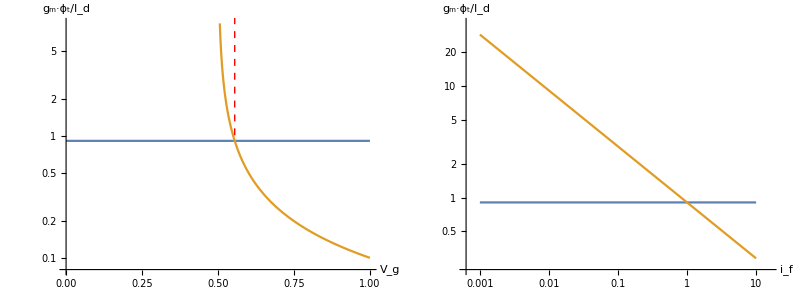

```mathematica
Block[{ϕt=0.025, n=1.1, Vs=0.0, Vth=0.5},
VgSpecRule=NSolve[gmPhiTIdWI[n]==gmPhiTIdSI[Vg, Vth, Vs, n, ϕt], Vg];
VgSpec = Replace[Vg, VgSpecRule⟦1⟧];
lineStyle={Red,Dashed};
line1=Line[{{VgSpec,0.01},{VgSpec,10}}];
Grid[{{
LogPlot[{gmPhiTIdWI[n],gmPhiTIdSI[Vg, Vth, Vs, n, ϕt]}, {Vg,0,1},ImageSize->Medium,AxesLabel->{"V_g","g_m·ϕ_t/I_d"},
 Epilog->{Directive[lineStyle],line1}],
LogLogPlot[{gmPhiTIdWI[n],gmPhiTIdSI[Vgif[if,Vth,Vs,n,ϕt], Vth, Vs, n, ϕt]}, {if,0.001,10},
ImageSize->Medium,AxesLabel->{"i_f","g_m·ϕ_t/I_d"}]
}}]
]
```

The solution below is where the two asymptote equations equal each other.

```mathematica
Solve[gmPhiTIdWI[n]==gmPhiTIdSI[Vg, Vth, Vs, n, ϕt], Vg]
```

{{Vg→n Vs+Vth+2 n ϕt}}

```mathematica
Block[{ϕt=0.025, n=1.1, Vs=0, Vth=0.5},
Solve[gmPhiTIdWI[n]==gmPhiTIdSI[Vg, Vth, Vs, n, ϕt], Vg]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Vg→0.555}}

UTSOIx Model

In this section, I try to trace through the math that fundamentally create the UTSOI1, UTSOI2, and UTSOI2.1 models that are used in STMicro’s PDK.

### Solve Poisson’s equation

We first start with the 1-D Poisson’s equation for an undoped silicon region, where x designates the direction going deeper into the body.  For convenience, we call x=0, as the point at which the front oxide meets the silicon body.
	(ⅆ^2 ϕ)/(ⅆ x^2)=-ρ/ϵ_Si; ρ=-q n, n=n_i ⅇ^((ϕ-V_c)/ϕ_t)
	(ⅆ^2 ϕ)/(ⅆ x^2)=(q n_i ⅇ^((ϕ-V_c)/ϕ_t))/ϵ_Si=β ⅇ^(ϕ/α); β=(q n_i ⅇ^(-V_c/ϕ_t))/ϵ_Si,α=ϕ_t
Based on this equation, we perform only the first integration, such that
	∫(ⅆ^2 ϕ)/(ⅆ x^2)=ⅆϕ/ⅆx
To solve for this integral, we take a quick side trip to solve for ϕ(x) and thereby solve for ϕ’(x).  We know from experience that the solution for ϕ(x) is of the form ϕ(x)=A log(B x).  Therefore the following equations are true:
	ϕ=A log(B x)
	ⅆϕ/ⅆx=A 1/x
	(ⅆ^2 ϕ)/(ⅆ x^2)=-A 1/x^2
To get somewhere with this equation, we use the first we equation, to solve for 1/x.
	ϕ=A log(B x)
	ϕ/A=log (B x)
	ⅇ^(ϕ/A)=B x
	1/x=B ⅇ^(-ϕ/A)
We can plug this back into the first and second derivative equations of ϕ(x):
	ⅆϕ/ⅆx=A B ⅇ^(-ϕ/A)
	(ⅆ^2 ϕ)/(ⅆ x^2)=-A B^2 ⅇ^((-2ϕ)/A)
We can now set the second derivative equal to our initial equation to solve for A and B:
	(ⅆ^2 ϕ)/(ⅆ x^2)=-A B^2 ⅇ^((-2ϕ)/A)=β ⅇ^(ϕ/α)
	∴ α=-A/2→ A=-2α
       β=-A B^2 = 2α B^2→ B=√(β/(2α)) 
If we plug the values of A and B back into our original equations we have the first and second integrals of the Poisson’s equation that we started out with:
	ϕ=(-2α )log(√(β/(2α)) x)
	ⅆϕ/ⅆx=(-2α) √(β/(2α)) ⅇ^(-ϕ/(-2α))=- √(2α β) ⅇ^(ϕ/(2α))
       =- √(2 ϕ_t (q n_i ⅇ^(-V_c/ϕ_t))/ϵ_Si) ⅇ^(ϕ/(2 ϕ_t))
	(ⅆ^2 ϕ)/(ⅆ x^2)=-(-2α) (√(β/(2α)))^2 ⅇ^((-2ϕ)/(-2α))= β ⅇ^(ϕ/α)
         = (q n_i ⅇ^(-V_c/ϕ_t))/ϵ_Si ⅇ^(ϕ/ϕ_t)
To get to the last step, we solve for the first integration in terms of electric field, where we know from Gauss’s law that E=-ⅆϕ/ⅆx:
	ⅆϕ/ⅆx=- √(2 ϕ_t (q n_i ⅇ^(-V_c/ϕ_t))/ϵ_Si) ⅇ^(ϕ/(2 ϕ_t))
	E= √((2 ϕ_t q n_i ⅇ^(-V_c/ϕ_t))/ϵ_Si) ⅇ^(ϕ/(2 ϕ_t))
	E^2=  (2 ϕ_t q n_i)/ϵ_Si ⅇ^((ϕ-V_c)/ϕ_t)
If we evaluate the difference in the electric field from the front surface to the back surface, this equals the same equation that is written in the UTSOI1 presentation [1].

E_sf^2-E_sb^2=  (2 ϕ_t q n_i)/ϵ_Si( ⅇ^((ϕ_sf-V_c)/ϕ_t)-  ⅇ^((ϕ_sb-V_c)/ϕ_t))

### Establish boundary conditions

Using Gauss’ Law, we are able to get two boundary conditions, one for the front surface and one for the back surface:
	E_sf=-C_ox/ϵ_Si(V_gf-V_FBf-ϕ_sf)
	E_sb=-C_box/ϵ_Si(V_gb-V_FBb-ϕ_sb)

### Account for interface coupling

Because the back gate also affects the front surface potential (assuming the channel depth is very thin), we know that there is an effect by ϕ_sb upon ϕ_sf.  Using a simple capacitor divdier, we are able to account for this affect.  The result of solving for this capacitor divider gives the following equation:
	ϕ_sb=C_Si/(C_Si+C_box)ϕ_sf+C_box/(C_Si+C_box)(V_gb-V_FBb)
	ϕ_sb=α_C ϕ_sf+ϵ; α_C=C_Si/(C_Si+C_box), ϵ=C_box/(C_Si+C_box)(V_gb-V_FBb)

### Surface potential equation

If we take the solutions of Poisson’s equation, the boundary conditions, and the interface coupling effects and put them together, we get the following result for our surface potential equation.  It should be noted that this equation is now dimensionless by dividing everything by ϕ_t, the thermal voltage:
	(x_gf-x_sf)^2-C_box^2/C_ox^2(α_c^2(x_gb-x_sf))^2=γ^2/ϕ_t(ⅇ^(x_sf-x_c)-ⅇ^(α_c x_sf+(1-α_c)x_gb-x_c))
	x_sf=ϕ_sf/ϕ_t, x_gf=(V_gf-V_FBf)/ϕ_t, x_gb=(V_gb-V_FBb)/ϕ_t, x_c=V_c/ϕ_t, α_C=C_Si/(C_Si+C_box), γ=(√(2 q ϵ_Si n_i))/C_ox

### Try to solve this surface potential equation for a relationship between x_gf and x_sf

```mathematica
FullSimplify[Solve[(xgf-xsf)^2-Cbox^2/Cox^2 αc^2(xgb-xsf)^2==γ^2/ϕt(ⅇ^(xsf-xc)-ⅇ^(αc xsf+(1-αc)xgb-xc)),xgf]]
D[FullSimplify[Solve[(xgf-xsf)^2-Cbox^2/Cox^2 αc^2(xgb-xsf)^2==γ^2/ϕt(ⅇ^(xsf-xc)-ⅇ^(αc xsf+(1-αc)xgb-xc)),xgf]],xsf]
```

{{xgf→xsf-(√(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb αc+xsf αc)) γ^2+Cbox^2 ⅇ^xc (xgb-xsf)^2 αc^2 ϕt)))/(Cox √ϕt)},{xgf→xsf+(√(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb αc+xsf αc)) γ^2+Cbox^2 ⅇ^xc (xgb-xsf)^2 αc^2 ϕt)))/(Cox √ϕt)}}

{{0→1-(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb αc+xsf αc) αc) γ^2-2 Cbox^2 ⅇ^xc (xgb-xsf) αc^2 ϕt))/(2 Cox √ϕt √(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb αc+xsf αc)) γ^2+Cbox^2 ⅇ^xc (xgb-xsf)^2 αc^2 ϕt)))},{0→1+(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb αc+xsf αc) αc) γ^2-2 Cbox^2 ⅇ^xc (xgb-xsf) αc^2 ϕt))/(2 Cox √ϕt √(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb αc+xsf αc)) γ^2+Cbox^2 ⅇ^xc (xgb-xsf)^2 αc^2 ϕt)))}}

```mathematica
Manipulate[
Csi=CFnActϵ[ϵsi,tsi];
Cox=CFnActϵ[ϵox,tox];
Cbox=CFnActϵ[ϵox,tbox];
curαc = αc[Csi,Cbox];
curγ=γFn[ϵsi,niFn[T],Cox];
ϕt=ϕT[T];
Grid[{
{Row[{"C_Si", "C_ox", "C_box"}, "\t"]},
{Row[{Csi, Cox, Cbox}, "\t"]},
{Plot[{
xsf+(√(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb curαc+xsf curαc)) curγ^2+Cbox^2 ⅇ^xc (xgb-xsf)^2 curαc^2 ϕt)))/(Cox √ϕt),
xsf-(√(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb curαc+xsf curαc)) curγ^2+Cbox^2 ⅇ^xc (xgb-xsf)^2 curαc^2 ϕt)))/(Cox √ϕt),
0.8/ϕt
},
{xsf,-xLim,xLim},AxesLabel->{"x_sf","x_gf"}, ImageSize->Medium,PlotRange->{-1.2/ϕt,1.2/ϕt}],
Plot[{
1+(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb curαc+xsf curαc) curαc) curγ^2-2 Cbox^2 ⅇ^xc (xgb-xsf) curαc^2 ϕt))/(2 Cox √ϕt √(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb curαc+xsf curαc)) curγ^2+Cbox^2 ⅇ^xc (xgb-xsf)^2 curαc^2 ϕt))),
1-(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb curαc+xsf curαc) curαc) curγ^2-2 Cbox^2 ⅇ^xc (xgb-xsf) curαc^2 ϕt))/(2 Cox √ϕt √(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb curαc+xsf curαc)) curγ^2+Cbox^2 ⅇ^xc (xgb-xsf)^2 curαc^2 ϕt)))
},
{xsf,-xLim,xLim},AxesLabel->{"x_sf","n (ⅆSubscriptBox[x, gf]/ⅆSubscriptBox[x, sf])"}, ImageSize->Medium]
}}],
{{xgb,-40,"x_gb"},-120,40},
{{xc,0,"x_c"},-2,2},
{{T,25},0,50},
{{tox,2.818 10^-9,"t_ox"},1.2263 10^-9,10 10^-9},
{{tsi,7 10^-9,"t_si"},2 10^-9,10 10^-9},
{{tbox,25 10^-9,"t_box"},20 10^-9,50 10^-9},
{{xLim,40},1,50}
]
```

3D Plot of x_gf as a function of x_sf and x_gb

```mathematica
Manipulate[
Csi=CFnActϵ[ϵsi,tsi];
Cox=CFnActϵ[ϵox,tox];
Cbox=CFnActϵ[ϵox,tbox];
curαc = αc[Csi,Cbox];
curγ=γFn[ϵsi,niFn[T],Cox];
ϕt=ϕT[T];
Plot3D[{
xsf+(√(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb curαc+xsf curαc)) curγ^2+Cbox^2 ⅇ^xc (xgb-xsf)^2 curαc^2 ϕt)))/(Cox √ϕt),
xsf-(√(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb curαc+xsf curαc)) curγ^2+Cbox^2 ⅇ^xc (xgb-xsf)^2 curαc^2 ϕt)))/(Cox √ϕt)},
{xsf,-10,40},{xgb,-40,10},AxesLabel->{"x_sf","x_gb","x_gf"}, Boxed->False],
{{xsf,10,"x_gb"},-120,10},
{{xc,0,"x_c"},-2,2},
{{T,25},0,50},
{{tox,2.818 10^-9,"t_ox"},1.2263 10^-9,10 10^-9},
{{tsi,7 10^-9,"t_si"},2 10^-9,10 10^-9},
{{tbox,25 10^-9,"t_box"},20 10^-9,50 10^-9},
{{xLim,100},10,120}
]
```

3D Plot of the n as a function of x_sf and x_gb

```mathematica
Manipulate[
Csi=CFnActϵ[ϵsi,tsi];
Cox=CFnActϵ[ϵox,tox];
Cbox=CFnActϵ[ϵox,tbox];
curαc = αc[Csi,Cbox];
curγ=γFn[ϵsi,niFn[T],Cox];
ϕt=ϕT[T];
Grid[{
{Plot3D[{
1+(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb curαc+xsf curαc) curαc) curγ^2-2 Cbox^2 ⅇ^xc (xgb-xsf) curαc^2 ϕt))/(2 Cox √ϕt √(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb curαc+xsf curαc)) curγ^2+Cbox^2 ⅇ^xc (xgb-xsf)^2 curαc^2 ϕt))),
1-(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb curαc+xsf curαc) curαc) curγ^2-2 Cbox^2 ⅇ^xc (xgb-xsf) curαc^2 ϕt))/(2 Cox √ϕt √(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb curαc+xsf curαc)) curγ^2+Cbox^2 ⅇ^xc (xgb-xsf)^2 curαc^2 ϕt)))
},
{xsf,-xLim,xLim},{xgb,-xLim1,xLim1},AxesLabel->{"x_sf","x_gb","n (ⅆSubscriptBox[x, gf]/ⅆSubscriptBox[x, sf])"}, ImageSize->Large,
PlotPoints->100,PlotRange->{1.10,1.11}]
}}],
(*{{xsf,10,"x_sf"},-40,40},*)
{{xc,0,"x_c"},-2,2},
{{T,25},0,50},
{{tox,2.818 10^-9,"t_ox"},1.2263 10^-9,10 10^-9},
{{tsi,7 10^-9,"t_si"},2 10^-9,10 10^-9},
{{tbox,25 10^-9,"t_box"},20 10^-9,50 10^-9},
{{xLim,22},10,50},
{{xLim1,50},10,120}
]
```

Shows that the “dead region when x_gb and x_sf are large is b/c the result is purely imaginary.

```mathematica
Manipulate[
Csi=CFnActϵ[ϵsi,tsi];
Cox=CFnActϵ[ϵox,tox];
Cbox=CFnActϵ[ϵox,tbox];
curαc = αc[Csi,Cbox];
curγ=γFn[ϵsi,niFn[T],Cox];
ϕt=ϕT[T];
Grid[{
{{
1+(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb curαc+xsf curαc) curαc) curγ^2-2 Cbox^2 ⅇ^xc (xgb-xsf) curαc^2 ϕt))/(2 Cox √ϕt √(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb curαc+xsf curαc)) curγ^2+Cbox^2 ⅇ^xc (xgb-xsf)^2 curαc^2 ϕt))),
1-(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb curαc+xsf curαc) curαc) curγ^2-2 Cbox^2 ⅇ^xc (xgb-xsf) curαc^2 ϕt))/(2 Cox √ϕt √(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb curαc+xsf curαc)) curγ^2+Cbox^2 ⅇ^xc (xgb-xsf)^2 curαc^2 ϕt)))
}}}],
{{xsf,35,"x_sf"},-40,40},
{{xgb,40,"x_gb"},-40,40},
{{xc,0,"x_c"},-2,2},
{{T,25},0,50},
{{tox,2.818 10^-9,"t_ox"},1.2263 10^-9,10 10^-9},
{{tsi,7 10^-9,"t_si"},2 10^-9,10 10^-9},
{{tbox,25 10^-9,"t_box"},20 10^-9,50 10^-9},
{{xLim,22},10,50},
{{xLim1,50},10,120}
]
```

### Account for inversion charge

Slope Factor as function of C_Si

```mathematica
Manipulate[
LogLinearPlot[sfFDSOI[Csi, Cox, Cbox], {Csi, 10^-2, 1}, AxesLabel->{"C_Si", "n"}, PlotRange->All],
{{Cox,10^-1},.0001, 1},
{{Cbox,10^-2},10^-4,10^-2}
]
```

Wavelength calculation

In this section, I use the potential energy to jump from the valence band to the conduction band to calculate the wavelength of an electron in silicon. If this wavelength is larger than the width of our transistors, then we start to suffer from quantum confinement.

### Plot temperature relation to bandgap voltage

```mathematica
Manipulate[
Grid[{
{Row[{QuantityMagnitude[UnitConvert[Quantity[N[tempC],"Celsius"],"Kelvins"]],"\t",Eg[QuantityMagnitude[UnitConvert[Quantity[tempC,"Celsius"],"Kelvins"]],Eg0Si,αSi,βSi]}]},
{Show[{
Plot[Eg[T,Eg0Si,αSi,βSi],{T,0,400}, ImageSize->Medium,AxesLabel->{"T (°K)","E_g (eV)"}],
ListPlot[{
{QuantityMagnitude[UnitConvert[Quantity[tempC,"Celsius"],"Kelvins"]],
Eg[QuantityMagnitude[UnitConvert[Quantity[tempC,"Celsius"],"Kelvins"]],Eg0Si,αSi,βSi]}},
PlotStyle->Directive[PointSize[Medium],Red]]
}]}}],
{{tempC,25, "T(°C)"},0,50, Appearance->{"Labeled","Open"}}
]
```

### Calculate the electron' s wavelength to jump the Energy band gap

```mathematica
Manipulate[
UnitConvert[
λe[Quantity[Eg[QuantityMagnitude[UnitConvert[Quantity[tempC,"Celsius"],"Kelvins"]],Eg0Si,αSi,βSi],"eV"],
Entity["Particle","Electron"][EntityProperty["Particle","Mass"]]],"SIBase"],
{{tempC,25, "T(°C)"},0,50, Appearance->{"Labeled","Open"}}
]
```

Plot of i_f vs q_is  (Inaccurate, needs to be revised)

This section will plot the relationship between drift current and diffusion current, as defined by S&GM
i_f=q_is^2+2 q_is

```mathematica
if[Idrift_,Idiffusion_]:=Idrift+Idiffusion
idrift[qis_]:=qis^2
idiff[qis_]:=2qis
```

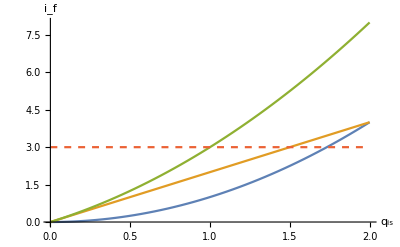

```mathematica
Plot[{idrift[qis],idiff[qis],if[idrift[qis],idiff[qis]],3},{qis,0,2},AxesLabel->{"q_is","i_f"},PlotStyle->{Directive[],Directive[],Directive[],Dashed}]
```

Plot of ϕ_F vs doping concentration

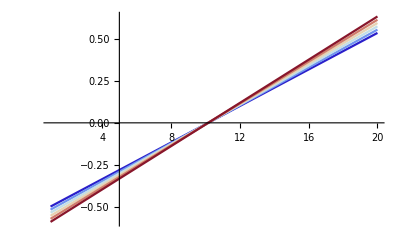

```mathematica
Block[{ni=1.45 10^10},
ϕFFunctions=Table[ϕT[T]Log[10^NaPow/ni],{T,0,50,10}];
Plot[ϕFFunctions,{NaPow,1,20}, PlotStyle->Table[ColorData["ThermometerColors",i/(Length[ϕFFunctions]-1)],{i,0,Length[ϕFFunctions]-1}]
]
]
```

Calculation of various transistor properties

```mathematica
coxegN=Cox[ϵo,Εox,toxegn];
coxegP=Cox[ϵo,Εox,toxegp];
csi=Csi[ϵsi,Εsi,tsi];
cbox=Cbox[ϵox,tbox];
megN = M[coxegN,csi,cbox];
megP = M[coxegP,csi,cbox];
Manipulate[
Grid[{
{Text["ϕ_F="],ϕF[ϕT[T],Nsi,ni[T]]},
{Text["C_oxegN'="],coxegN,Text["C_oxegP'="],coxegP},
{Text["C_oxN'="],coxN,Text["C_oxP'="],coxP},
{Text["C_oxegN="],coxegN*WegN*LegN,Text["C_oxegP="],coxegP*WegP*LegP},
{Text["C_oxN="],coxN*WN*LN,Text["C_oxP="],coxP*WP*LP},
{Text["m_egN="],megN, Text["m_egP="],megP},
{Text["C_si="],csi,Text["C_box="],cbox}
}],
{{T,25,"T (°C)"}, 0,50,5,Appearance->{"Labeled","Open"}},
{{Nsi,1. 10^10,"N_si"},Table[1. 10^i,{i,0,20,1}]}
]
```

Why are the capacitance values for the oxide larger than 1fF?

This section below, just shows that if you have capacitors in series, the maximum effective capacitance size is the minimum of the capacitors in series.  This means that C_ox can be on the order of 1-5fF, but the effective capacitance of a single MOSCAP device be as low as 140aF.

```mathematica
Ceff[C1_,C2_]:=(1/C1+1/C2)^-1
```

```mathematica
Manipulate[
Grid[{
{Ceff[C1,C2]},
{Show[
Plot[Ceff[C1,C2],{C1,0,10},AxesLabel->{"C_1","C_eff"},ImageSize->500,PlotRange->All],
ListPlot[{{C1,Ceff[C1,C2]}},PlotStyle->PointSize[Large]]
]}
}],
{{C1,0.5},0,10,0.1,Appearance->"Labeled"},
{{C2,0.5},0,10,0.1,Appearance->"Labeled"}
]
```

Temperature effect on n_i

This shows that the intrinsic doping constant changes with temperature.  Note: As you increase temperature, you increase the intrinsic carrier concentration, which makes sense because you have more thermal energy causing electrons to bounce around and be carriers.

```mathematica
{ni[0],ni[20],ni[25],ni[30],ni[50]}
```

{1.20145×10^9,7.71439×10^9,1.18235×10^10,1.78752×10^10,8.24833×10^10}

In the plot below, we show that as you increase temperature, you see that ϕ_F decreases.

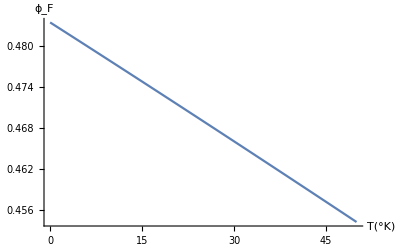

```mathematica
Block[{Nb=10^18},
Plot[{ϕF[ϕT[T],Nb,ni[T]]}, {T,0,50}, AxesLabel->{"T(°K)", "ϕ_F"}]
]
```

Debye length in semiconductors

```mathematica
Ld[Nd_,ϕt_,ϵ_,q_]:=√((ϵ ϕt)/(q Nd))
```

In the plot below, I try to model how the Debye length changes as a function of the doping concentration, N_d.  The Debye length for semiconductors is modeled as L_D=√((ϵ ϕ_t)/(q N_d)).  Unit analysis of this says that  √((F/m V)/(C atoms/m^2))→√((C m^2)/(m C atoms))→√(m/atom), which doesn’t make sense.  It should be in units of m.  Thd Debye length is the length at which electrostatic effects wears off.  Note: this length assumes that the electrostatic effects have a discrete distance away from the source of the electric field at which no effect takes place, but in reality this is a continuous spectrum and this point is a rough approximation of where the effects are negligible.

```mathematica
Manipulate[
Block[{ϵsi=1.045 10^-10},
Ld==Ld[10^Nd,ϕT[T],ϵsi,QuantityMagnitude[UnitConvert[Null,"Coulomb"]]]
],
{{T,25,"T"},0,50,5,Appearance->{"Labeled","Open"}},
{{Nd,10,"N_d"},0,20,0.5,Appearance->{"Labeled","Open"}}
]
```

## Appendix

```mathematica
Integrate[ⅇ^(a x),x]
D[ⅇ^(a x),x]
```

ⅇ^(a x)/a

a ⅇ^(a x)

Front surface gate voltage as a function of surface potential and back-gate voltage

```mathematica
xgfP[xsf_,xgb_,xc_,Csi_,Cox_,Cbox_, T_,ϵsi_]:=
xsf+(√(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb αc[Csi,Cbox]+xsf αc[Csi,Cbox])) γFn[ϵsi,niFn[T],Cox]^2+Cbox^2 ⅇ^xc (xgb-xsf)^2 αc[Csi,Cbox]^2 ϕT[T])))/(Cox √ϕT[T])
xgfN[xsf_,xgb_,xc_,Csi_,Cox_,Cbox_, T_,ϵsi_]:=
xsf-(√(ⅇ^-xc (Cox^2 (ⅇ^xsf-ⅇ^(xgb-xgb αc[Csi,Cbox]+xsf αc[Csi,Cbox])) γFn[ϵsi,niFn[T],Cox]^2+Cbox^2 ⅇ^xc (xgb-xsf)^2 αc[Csi,Cbox]^2 ϕT[T])))/(Cox √ϕT[T])
```